## Nuclear potentials with spherical symmetry

### Woods-Saxon Potential

```mathematica
vWS[r_,a_,v0_,R_]:=-v0/(1+Exp[(r-R)/a]);
pWS[a_,v0_,R_]:=Plot[vWS[x,a,v0,R],{x,-10,10}];
```

### Harmonic oscillator potential

```mathematica
vHO[r_,ω0_,M_,ϵ_]:=(M*ω0^2)/2 r^2+ϵ;
pHO[ω0_,M_,ϵ_]:=Plot[vHO[x,ω0,M,ϵ],{x,-10,10}];
```

### Finite square-well

```mathematica
vFSQ[r_,v0_,R_]:=Piecewise[{{-v0, r≤R}, {0, r>R}}];
pFSQ[v0_,R_]:=Plot[vFSQ[x,v0,R],{x,-10,10}];
```

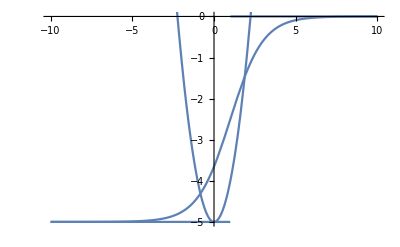

```mathematica
Show[pWS[1,5,1],pFSQ[5,1],pHO[1,2,-5]]
```